# A336815 - Mathematica code

Add four functions.
Loop through these with a iterative loop

//1. outswing ball 5, add value of 1 to ball 5, sum 1-4       
//2. drop right ball and add value to #4 + sum 1-5
//3. outswing ball 1, add value 5 to that ball, sum 2-5
//4. drop ball 1, add value of 1 to 2, sum 1-5

define balls array

```mathematica
count = 15;BallSumList = {};BallList = {0,0,0,0,1};
AddValue[ball_, Add_] :=BallList[[ball]] += BallList[[Add]];
SumValue[from_,to_] := AppendTo[BallSumList,Sum[BallList[[i]],{i,from,to}]];
Do[(
AddValue[5,1];SumValue[1,4];
AddValue[4,5];SumValue[1,5];
AddValue[1,5];SumValue[2,5];
AddValue[2,1];SumValue[1,5];
),
{k,1,count,1}];
Print[BallSumList];
```

{0,2,2,4,3,7,6,12,10,20,17,33,28,54,46,88,75,143,122,232,198,376,321,609,520,986,842,1596,1363,2583,2206,4180,3570,6764,5777,10945,9348,17710,15126,28656,24475,46367,39602,75024,64078,121392,103681,196417,167760,317810,271442,514228,439203,832039,710646,1346268,1149850,2178308,1860497,3524577}

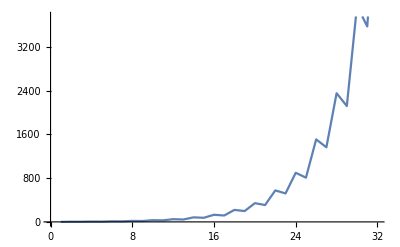

```mathematica
ListLinePlot[{0,3,3,6,5,11,10,18,16,31,28,49,44,83,75,130,117,219,198,342,308,575,520,897,808,1507,1363,2350,2117,3947,3570,6154}]
```

```mathematica
count = 15;
BallSumList = {};
BallIndexList = {};
BallList = {0,0,0,0,1};
AddValue[ball_, Add_] :=BallList[[ball]] += BallList[[Add]];
AddBall[x_] := AppendTo[BallIndexList,BallList[[x]]];
Do[(
AddValue[5,1];AddBall[4];
AddValue[4,5];AddBall[4];
AddValue[1,5];AddBall[4];
AddValue[2,1];AddBall[4];
),
{k,1,count,1}];
Print[BallIndexList];
```

{0,1,1,1,1,3,3,3,3,8,8,8,8,21,21,21,21,55,55,55,55,144,144,144,144,377,377,377,377,987,987,987,987,2584,2584,2584,2584,6765,6765,6765,6765,17711,17711,17711,17711,46368,46368,46368,46368,121393,121393,121393,121393,317811,317811,317811,317811,832040,832040,832040}

Cf. A027941 (first occurrence of each distinct element, second ball).
Cf. A001906 (first occurrence of each distinct element, fourth ball).

```mathematica
count = 15;
BallSumList = {};
BallList = {0,0,0,0,1};
AddValue[ball_, Add_] :=BallList[[ball]] += BallList[[Add]];
SumValue[from_,to_] := AppendTo[BallSumList,Sum[BallList[[i]],{i,from,to}]];
Do[(
AddValue[5,1];SumValue[1,4];
AddValue[4,5];AddValue[3,5];SumValue[1,5];
AddValue[1,5];SumValue[2,5];
AddValue[2,1];AddValue[3,5];SumValue[1,5];
),
{k,1,count,2}];
Print[BallSumList];
```

{0,3,3,6,5,11,10,18,16,31,28,49,44,83,75,130,117,219,198,342,308,575,520,897,808,1507,1363,2350,2117,3947,3570,6154}